```mathematica
Get[NotebookDirectory[]<>#]&/@
{"load_takahashi.wl",
"styles.wl"
};
```

## Fit temperature deactivation

```mathematica
FvFmMax=0.65;
fit0={αU->0.5 10^9};
fit1=NSolve[FvFmMax==αPtotalP/(αU+αPtotalP)/.fit0][[1]]~Join~fit0
```

{αPtotalP→9.28571×10^8,αU→5.×10^8}

```mathematica
αPxxx=αPtotalP ρT/(ρT+xTref1  ⅇ^(-σT1/(w+273))/ⅇ^(-σT1/(wRef+273))+xTref2  ⅇ^(-σT2/(w+273))/ⅇ^(-σT2/(wRef+273)));
FvFmFunc=αPxxx/(αU+αPxxx);
```

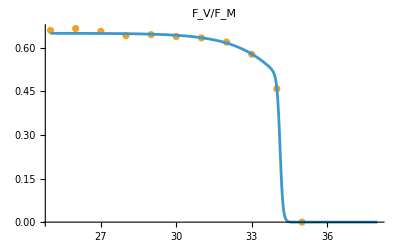

{αPtotalP→9.28571×10^8,αU→5.×10^8,σT1→75880.5,σT2→1.62172×10^6,ρT→0.001,xTref1→0.00175396,xTref2→11271.5,wRef→35.}

FittedModel::constr: The property values {AIC} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

-64.7881

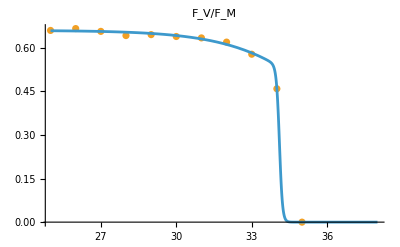

{αPtotalP→9.70588×10^8,αU→5.×10^8,σT1→48719.6,σT2→1.58029×10^6,ρT→0.001,xTref1→0.00110034,xTref2→11401.,wRef→35.}

FittedModel::constr: The property values {AIC} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

-69.2656

```mathematica
(*FvFmScaling[W_]:=FvFmMax fT[W];*)

FvFmDarkData=Normal[data["FigS1"][Select[#["h"]==0.5&]][All,{#["temp"],#["Fv/Fm"]}&]](*Table[Normal[data["FigS1"][Select[#["h"]==hour&]][All,{#["temp"],#["Fv/Fm"]}&]],{hour,{0.5(*,3.5*)}}]*);
FvFmTempFit=Quiet@NonlinearModelFit[FvFmDarkData, 
{FvFmFunc/.fit1,ρT==10^-3,wRef==35,σT1>0,(*1.4 10^6>*)σT2>0,xTref1>0,xTref2>0},{{σT1,10^5},{σT2,10^6},{ρT,10^-3},{xTref1,10^-3},{xTref2,10^4},{wRef,35}},w];
Row[{
Show[
ListPlot[FvFmDarkData,AxesOrigin->{Automatic},PlotStyle->{{Dashed,ColorData[116][2]}(*,{Dashed,ColorData[116][3]}*)},Joined->False,FrameLabel->{{None,None},{w/.units,None}}(*PlotLegends->Placed[{"data"},Right],*)],
Plot[FvFmTempFit[W](*Evaluate[FvFmScaling[W]/.FvFmTempFit["BestFitParameters"]]*),{W,25,38},Evaluate@style(*,PlotLegends->Placed[{"model"},Right]*)],PlotRange->All,FrameLabel->{{None,None},{w/.units,None}},PlotLabel->"F_V/F_M"]}]
Join[fit1,FvFmTempFit["BestFitParameters"]]
FvFmTempFit["AIC"]
```

## Can we simplify? remove two xTref and asume mutliplicative effect - no!

```mathematica
FvFmMax=0.66;
fit0={αU->0.5 10^9};
fit1=NSolve[FvFmMax==αPtotalP/(αU+αPtotalP)/.fit0][[1]]~Join~fit0
```

{αPtotalP→9.70588×10^8,αU→5.×10^8}

```mathematica
αPxxx=αPtotalP ρT/(ρT+xTref  ⅇ^(-σT1/(w+273))/ⅇ^(-σT1/(wRef+273))  ⅇ^(-σT2/(w+273))/ⅇ^(-σT2/(wRef+273)));
FvFmFunc=αPxxx/(αU+αPxxx);
```

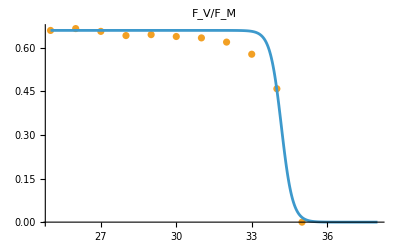

{αPtotalP→9.70588×10^8,αU→5.×10^8,σT1→211571.,σT2→211571.,ρT→0.001,xTref→0.115927,wRef→35.}

```mathematica
(*FvFmScaling[W_]:=FvFmMax fT[W];*)

FvFmDarkData=Normal[data["FigS1"][Select[#["h"]==0.5&]][All,{#["temp"],#["Fv/Fm"]}&]](*Table[Normal[data["FigS1"][Select[#["h"]==hour&]][All,{#["temp"],#["Fv/Fm"]}&]],{hour,{0.5(*,3.5*)}}]*);
FvFmTempFit=Quiet@NonlinearModelFit[FvFmDarkData, 
{FvFmFunc/.fit1,ρT==10^-3,wRef==35,σT1>0,(*1.4 10^6>*)σT2>0,xTref>0},{{σT1,1},{σT2,2},{ρT,10^-3},{xTref,.01},{wRef,35}},w];
Row[{
Show[
ListPlot[FvFmDarkData,AxesOrigin->{Automatic},PlotStyle->{{Dashed,ColorData[116][2]}(*,{Dashed,ColorData[116][3]}*)},Joined->False,FrameLabel->{{None,None},{w/.units,None}}(*PlotLegends->Placed[{"data"},Right],*)],
Plot[FvFmTempFit[W](*Evaluate[FvFmScaling[W]/.FvFmTempFit["BestFitParameters"]]*),{W,25,38},Evaluate@style(*,PlotLegends->Placed[{"model"},Right]*)],PlotRange->All,FrameLabel->{{None,None},{w/.units,None}},PlotLabel->"F_V/F_M"]}]
Join[fit1,FvFmTempFit["BestFitParameters"]]
```

## Alternative: single Arrhenius

```mathematica
FvFmMax=0.66;
fit0={αU->0.5 10^9};
fit1=NSolve[FvFmMax==αPtotalP/(αU+αPtotalP)/.fit0][[1]]~Join~fit0
```

{αPtotalP→9.70588×10^8,αU→5.×10^8}

```mathematica
αPxxx=αPtotalP ρT/(ρT+xTref  ⅇ^(-σT/(w+273))/ⅇ^(-σT/(wRef+273)));
FvFmFunc=αPxxx/(αU+αPxxx);
```

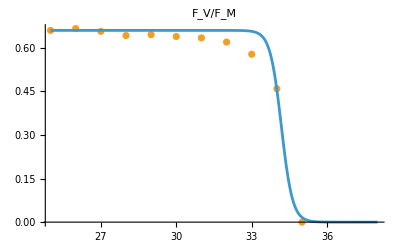

{αPtotalP→9.70588×10^8,αU→5.×10^8,σT→423134.,xTref→0.115916,ρT→0.001,wRef→35.}

```mathematica
(*FvFmScaling[W_]:=FvFmMax fT[W];*)

FvFmDarkData=Normal[data["FigS1"][Select[#["h"]==0.5&]][All,{#["temp"],#["Fv/Fm"]}&]](*Table[Normal[data["FigS1"][Select[#["h"]==hour&]][All,{#["temp"],#["Fv/Fm"]}&]],{hour,{0.5(*,3.5*)}}]*);
FvFmTempFit=Quiet@NonlinearModelFit[FvFmDarkData, 
{FvFmFunc/.fit1,ρT==10^-3,wRef==35,(*1.4*)(*3 10^5>*)σT>0(*5 10^5*),xTref>0},{{σT,1},{xTref,.01},{ρT,10^-3},{wRef,35}},w];
Row[{
Show[
ListPlot[FvFmDarkData,AxesOrigin->{Automatic},PlotStyle->{{Dashed,ColorData[116][2]}(*,{Dashed,ColorData[116][3]}*)},Joined->False,FrameLabel->{{None,None},{w/.units,None}}(*PlotLegends->Placed[{"data"},Right],*)],
Plot[FvFmTempFit[W](*Evaluate[FvFmScaling[W]/.FvFmTempFit["BestFitParameters"]]*),{W,25,38},Evaluate@style(*,PlotLegends->Placed[{"model"},Right]*)],PlotRange->All,FrameLabel->{{None,None},{w/.units,None}},PlotLabel->"F_V/F_M"]}]
Join[fit1,FvFmTempFit["BestFitParameters"]]
```